## Brian — PS 18 — 2025-04-15 — Solution

## EIWL3 Sections 41 and 42 My solutions to 41.9 and 41.10 are broken.

## Exercises from EIWL3 Section 41

```mathematica
(* 41.1 *) Cases[IntegerDigits[Array[#^2&,100]],{___,x_,y_,___}/;x==y]
```

{{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}}

```mathematica
(* 41.2 *) StringJoin/@Cases[Array[Characters[RomanNumeral[#]]&,100],{___,"L",___,"I",___,"X",___}]
```

{XLIX,LIX,LXIX,LXXIX,LXXXIX}

```mathematica
(* 41.3 *) f[list_]:=Equal[list,Reverse[list]]
```

```mathematica
(* 41.4 *)  (* So as not to fill up my document, I just took the first 20: *)Take[Cases[Partition[TextWords[WikipediaData["alliteration"]],2,1],{x_,y_}/;Characters[x][[1]]==Characters[y][[1]]],20]
```

{{or,of},{as,a},{Peter,Piper},{pickled,peppers},{Irish,It},{as,an},{ideas,in},{Icelandic,It},{cartoon,characters},{the,term},{identical,initial},{several,special},{as,alliteration},{stressed,syllables},{as,an},{lazy,languid},{languid,line},{as,alliteration},{be,because},{such,syllables}}

```mathematica
{{"or","of"},{"as","a"},{"Peter","Piper"},{"pickled","peppers"},{"Irish","It"},{"as","an"},{"ideas","in"},{"Icelandic","It"},{"cartoon","characters"},{"the","term"},{"identical","initial"},{"several","special"},{"as","alliteration"},{"stressed","syllables"},{"as","an"},{"lazy","languid"},{"languid","line"},{"as","alliteration"},{"be","because"},{"such","syllables"}}
(* Notice that this solution is case-sensitive. One could also convert the *) (* characters to lower-case and then test to get a case-insensitive test. *)
```

{{or,of},{as,a},{Peter,Piper},{pickled,peppers},{Irish,It},{as,an},{ideas,in},{Icelandic,It},{cartoon,characters},{the,term},{identical,initial},{several,special},{as,alliteration},{stressed,syllables},{as,an},{lazy,languid},{languid,line},{as,alliteration},{be,because},{such,syllables}}

```mathematica
(* 41.5 *) Clear[x,y]; (* I was getting gibberish due to having defined x and y elsewhere. *)
FixedPointList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2}]//Grid
```

4 | 5 | 1 | 3 | 2
4 | 1 | 5 | 3 | 2
1 | 4 | 5 | 3 | 2
1 | 4 | 3 | 5 | 2
1 | 3 | 4 | 5 | 2
1 | 3 | 4 | 2 | 5
1 | 3 | 2 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5

```mathematica
(* 41.6 *) Clear[x,y];
Transpose[FixedPointList[#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y}&,RandomInteger[100,50]]]//ArrayPlot
```

-Graphics-

```mathematica
(* 41.7 *) FixedPoint[(#+2/#)/2&,1.0] (* This is a crafty way of computing Sqrt[2]. *)
```

1.41421

```mathematica
(* 41.8 *) FixedPointList[#/. {a_Integer,b_Integer}/;b!=0->{b,Mod[a,b]}&,{12345,54321}]
```

{{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}}

```mathematica
(* 41.9 *) Clear[x,y,z];
FixedPointList[#/.{{s[x_][y_][z_]->x[z][y[z]]},{k[x_][y_]->x}}&,s[s][k][s[s[s]][s]][s]]
```

$Aborted

```mathematica
(* 41.10 *)IntegerDigits[Factorial[100]]/.{leading_..,remainder_}/;leading>0->leading
```

{9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* 41.11 *)Length/@NestList[If[#[[1]]==1,Join[Drop[#,2],{0,1}],Join[Drop[#,2],{1,0,0}]]&,{1,0},200]
```

{2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125}

```mathematica
(* 41.12 *)switch[foo_]:=Module[{fooDropped=Drop[foo,2]},Switch[foo[[1]],0,Join[fooDropped,{2,1}],1,Append[fooDropped,0],2,Join[fooDropped,{0,2,1
,2}]]]
```

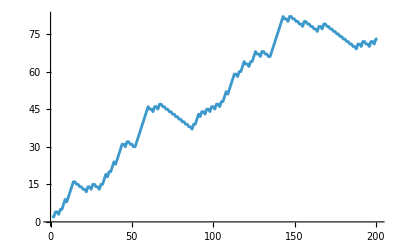

```mathematica
ListLinePlot[Length/@NestList[switch,{0,0},200]]
```

## Exercises from EIWL3 Section 42

```mathematica
(* 42.1 *) StringReplace["1 2 3 4"," "->"---"]
```

1---2---3---4

```mathematica
(* 42.2 *)
```

```mathematica
(* 42.3 *)
```

```mathematica
(* 42.4 *)
```

```mathematica
(* 42.5 *)
```

```mathematica
(* 42.6 *)
```

```mathematica
(* 42.7 *)
```

```mathematica
(* 42.8 *)
```